```mathematica
k=3;
```

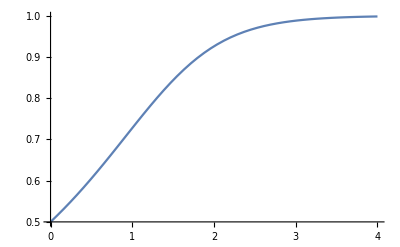

```mathematica
baseSol =NDSolve[{w'[t] ==w[t]^(k-1) - w[t]^(k+1), w[0]==0.5}, w[t], {t, 0, 100}];
Plot[w[t]/.baseSol,{t,0,4}]
```

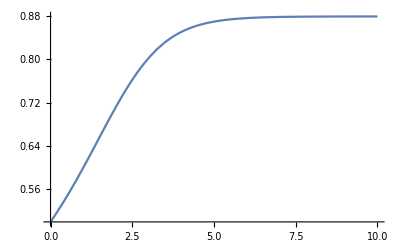

```mathematica
λ = 0.2;
constSol =NDSolve[{w'[t] ==w[t]^(k-1) - w[t]^(k+1) - λ*w[t], w[0]==0.5}, w[t], {t, 0, 10}];
Plot[w[t]/.constSol,{t,0,10}]
```

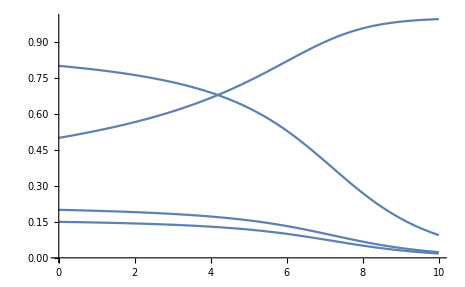

{0.0547192,0.015081,0.610176,0.24936}

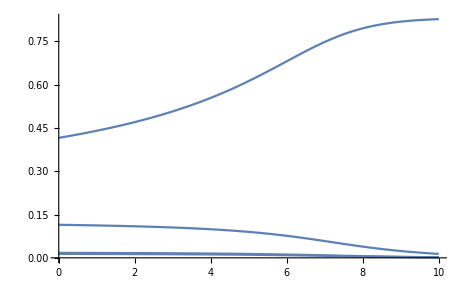

```mathematica
k=5;
{a1,a2,a3, a4}={0.2, 0.1,0.85, 0.895};
simulSol =NDSolve[{
w1'[t] ==a1^k*(w1[t]^(k-1) - w1[t]^(k+1) - w1[t]*((a2/a1*w2[t])^k + (a3/a1*w3[t])^k + (a4/a1*w4[t])^k)),
w2'[t] ==a2^k*(w2[t]^(k-1) - w2[t]^(k+1) - w2[t]*((a1/a2*w1[t])^k + (a3/a2*w3[t])^k + (a4/a2*w4[t])^k)),
w3'[t] ==a3^k*(w3[t]^(k-1) - w3[t]^(k+1) - w3[t]*((a2/a3*w2[t])^k + (a1/a3*w1[t])^k + (a4/a3*w4[t])^k)),
w4'[t] ==a4^k*(w4[t]^(k-1) - w4[t]^(k+1) - w4[t]*((a3/a4*w3[t])^k + (a1/a4*w1[t])^k + (a2/a4*w2[t])^k)),
w1[0]==0.2, w2[0]==0.8, w3[0]==0.15, w4[0]==0.5}, {w1[t], w2[t],w3[t],w4[t]}, {t, 0, 10}];
Plot[{w1[t], w2[t], w3[t], w4[t]}/.simulSol,{t,0,10}]
{a1, a2, a3, a4}^(k/(k-2)){0.8, 0.7, 0.8, 0.3}//N
Plot[{a1, a2, a3, a4}^(k/(k-2))*{w1[t], w2[t], w3[t], w4[t]}/.simulSol,{t,0,10}]
```

```mathematica
w1[t]^2 + w2[t]^2 + w3[t]^2+w4[t]^2/.simulSol/.t->10
```

{0.999335}

```mathematica
Assuming[Element[n, Integers]&&n>= 3&&0≤ a≤ 1,
DSolve[{w'[t] ==w[t]^(n-1) - w[t]^(n+1), w[0]==a}, w[t], t]]
```

{{w[t]→InverseFunction[(Hypergeometric2F1[1,1-n/2,2-n/2,#1^2] #1^(2-n))/(-2+n)&][-t+(a^(2-n) Hypergeometric2F1[1,1-n/2,2-n/2,a^2])/(-2+n)]}}

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{w[t]→(-0.333333+ⅇ^(2 t))/(0.333333+ⅇ^(2 t))}}

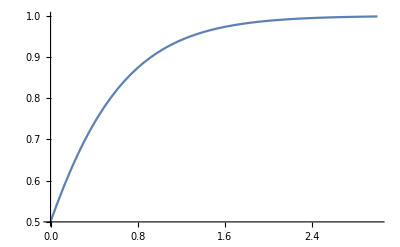

```mathematica
DSolve[{w'[t] ==1-w[t]^2, w[0]==0.5}, w[t], t]
Plot[w[t]/.%,{t,0,3}]
```

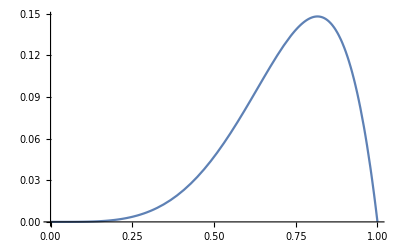

```mathematica
Plot[x^4(1-x^2), {x, 0, 1}]
```

```mathematica
Assuming[0<a<1,DSolve[{w'[t] ==1-w[t]^2, w[0]==a}, w[t], t]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{w[t]→(-1+a+ⅇ^(2 t)+a ⅇ^(2 t))/(1-a+ⅇ^(2 t)+a ⅇ^(2 t))}}

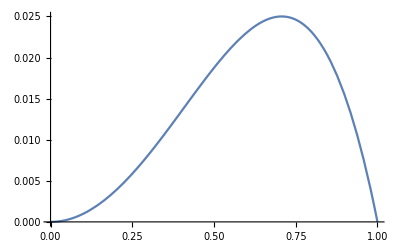

```mathematica
Plot[x^2(1-x^2) -0.9x^2*(1-x^2), {x,0, 1}]
```

```mathematica
1.75
```

1.75

```mathematica
Rationalize[1.75]
```

7/4